# Volume of the 3D Sphere without calculus

I make a derivation of the volume of the Sphere only with pre-calculus ideas.

Luis Antonio Vasquez Reina, Jun. 24,  2018

How does one get the volume of the sphere without knowing calculus? Simple forms like cubes and prisms are fairly straightforward to study, and when confronted with curved objects integral calculus is the go-to mathematical tool. Yet, people have known and studied rounded objects like spheres and paraboloids for centuries, thus there must be a way to proceed, and I will show how.

## Cavalieri’s Principle

Start by explaining the basics ...

Suppose we have two objects in 3D between two planes. For example, consider a cylinder.

We plot a cylinder of height 2 that starts at the origin and has radius 1

```mathematica
(myFirstCylinder=Cylinder[{{0,0,0},{0,0,2}},1])//Graphics3D
```

-Graphics3D-

Then, consider a slanted cylinder.

This takes a little more work to construct, first we make a right cylinder next to our original cylinder

```mathematica
mySlantedCylinder=Cylinder[{{3,3,0},{3,3,2}},1];
Graphics3D[{myFirstCylinder,mySlantedCylinder}]
```

-Graphics3D-

Now we will shear our new cylinder 30 degrees

```mathematica
mySlantedCylinder=GeometricTransformation[mySlantedCylinder,ShearingTransform[30 Degree,{1,0,0},{0,0,1}]];
Graphics3D[{myFirstCylinder,mySlantedCylinder}]
```

-Graphics3D-

Of course, this two cylinders are between two parallel planes.

To visualize this, we first make the cylinders somewhat transparent

```mathematica
myFirstCylinder={Opacity[0.4],myFirstCylinder};
mySlantedCylinder={Opacity[0.4],mySlantedCylinder};
```

And now we plot the two planes

```mathematica
upperPlane={Opacity[0.3],InfinitePlane[{0,0,2},{{1,0,0},{0,1,0}}]};  (*plane z=2*)
lowerPlane={Opacity[0.3],InfinitePlane[{0,0,0},{{1,0,0},{0,1,0}}]} ;     (*plane z=0*)
Graphics3D[ {myFirstCylinder,mySlantedCylinder, upperPlane, lowerPlane},
PlotRange->{{-1,6},{-1,6},{-0.5,2.5}}]
```

-Graphics3D-

Cavalieri' s principle states that, if every plane parallel to these two planes cuts the objects in sections of the same are, then they have the same volume. This is what happens in our example:

Here there is an animation of how the cuts look

```mathematica
Animate[
Graphics3D[ {myFirstCylinder,mySlantedCylinder, upperPlane,lowerPlane,
      {Opacity[0.6],Orange,InfinitePlane[{0,0,2*Abs[Sin[t]]},{{1,0,0},{0,1,0}}]} (*oscilating plane*)
},PlotRange->{{-1,6},{-1,6},{-0.5,2.5}}], 
{t,0,π,0.01}
]
```

## Volume of the sphere

### Making the 3D construction

As usually with dealing with mathematical object, now that we can use Cavalieri’s principle, we have to figure out an ingenious way to use it to solve our problem. Luckily, people have already figured that out for us.  Consider a sphere of radius ℛ.

Sphere or radius ℛ at the origin (we will graphic it as if ℛ is 2, but the argument holds for any ℛ, of course).

```mathematica
ℛ=2;
mySphere={Opacity[0.4],Sphere[{0,0,0},ℛ]}; (*sphere is at the origin*)
Graphics3D[mySphere]
```

-Graphics3D-

Now, draw a cylinder of height 2ℛ and radius ℛ next to the sphere

```mathematica
myCylinder={Opacity[0.1],Red,Cylinder[{{5,5,-ℛ},{5,5,ℛ}},ℛ]};
Graphics3D[{mySphere,myCylinder}]
```

-Graphics3D-

After that, we construct two cones inside the cylinder. Both cones have their top at the center of the sphere, and their bottoms are the extremes of the cylinder.

```mathematica
upperCone={Opacity[0.1],Blue,Cone[{{5,5,-ℛ},{5,5,0}},ℛ]};
lowerCone={Opacity[0.1],Blue,Cone[{{5,5,ℛ},{5,5,0}},ℛ]};
Graphics3D[{mySphere,myCylinder,upperCone,lowerCone}]
```

-Graphics3D-

We cut both objects with a plane

```mathematica
Animate[Graphics3D[{mySphere,myCylinder,upperCone,lowerCone,
{Opacity[0.4],Orange,InfinitePlane[{0,0,2*Sin[t]},{{1,0,0},{0,1,0}}]}},
PlotRange->{{-3,8},{-3,8},{-2.5,2.5}}
],{t,0,2π}]
```

The way to use Cavalieri’ s principle will be to study the regions that appear due to this cut. Specifically, the region inside the sphere and the region inside the cylinder but outside the cones.

### Looking at the cuts

If the plane is at a distance 𝒹 from the center of the cylinder, in the horizontal plane, we get a cut that consists of three circles.

Taking 𝒹=1.2 and a provisional radius for the circle that comes from the sphere:

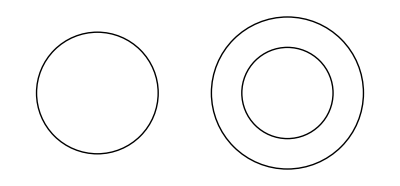

```mathematica
d=1.2;
Graphics[{Circle[{0,0},1.6], (*1.6 is a provisional radius*)
		Circle[{5,0},ℛ],
		Circle[{5,0},d]  }]
```

To get the exact dimensions of these circles, we will use another ingenious trick, notice that a vertical cut looks like this

Remember that the center of the cylinder is at {5,5,0}, this is why so many 5’s appear in the code.

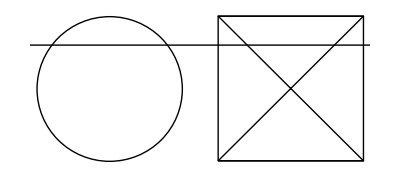

```mathematica
verticalCut=Graphics[{ 
Circle[{0,0},ℛ],
Line[{{5-ℛ,-ℛ},{5+ℛ,-ℛ},{5+ℛ,+ℛ},{5-ℛ,ℛ},{5-ℛ,-ℛ}}],
Line[{{5,0},{5+ℛ,ℛ},{5-ℛ,ℛ},{5,0}}],
Line[{{5,0},{5+ℛ,-ℛ},{5-ℛ,-ℛ},{5,0}}],
InfiniteLine[{{0,d},{5,d}}]        }]
```

Notice that the section of the cylinder is a square because we constructed the cylinder with radius ℛ and height 2ℛ. It is very useful to label this graphic:

Labeling can become cumbersome

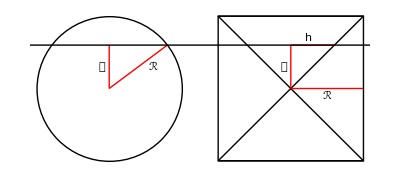

```mathematica
Show[verticalCut,
Graphics[{{Red,Line[{{0,0},{0,d}}]},Text["𝒹",{-0.2,d/2}]}],
Graphics[{{Red,Line[{{5,0},{5,d}}]},Text["𝒹",{5-0.2,d/2}]}],
Graphics[{{Red,Line[{{0,0},{Sqrt[ℛ^2-d^2],d}}]},Text["ℛ",{1+0.2,d/2}]}],
Graphics[{{Red,Line[{{5,d},{5+d,d}}]},Text["h",{5+0.5,d+0.2}]}],
Graphics[{{Red,Line[{{5,0},{7,0}}]},Text["ℛ",{5+1,-0.2}]}]      ]
```

By the Pythagorean Theorem, the radius of the circle in the cut of the sphere is √(ℛ^2-𝒹^2), also, since the section of the cylinder is a square, we have that h=d !

Now the horizontal cut looks like this:

Some numbers may appear random, they are used to get a good plot. Rest assure, this does not affect the argument in any way.

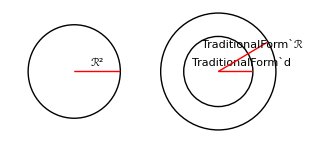

```mathematica
Show[Graphics[{Circle[{0,0},1.6], (*1.6 is a provisional radius*)
		Circle[{5,0},ℛ],
		Circle[{5,0},d]}],
	Graphics[{{Red,Line[{{0,0},{1.6,0}}]},Text["ℛ^2",{1.6/2,0.3}]}],
	Graphics[{{Red,Line[{{5,0},{5+1.2,0}}]},Text["TraditionalForm`d",{5+1.6/2,0.3}]}],
	Graphics[{{Red,Line[{{5,0},{5+1.7,1.0}}]},Text["TraditionalForm`ℛ",{5+1.2,0.9}]}] ]
```

The area of the horizontal cut of the sphere is π(ℛ^2-𝒹^2), and the horizontal cut of the region inside the cylinder but outside the cone has an area πℛ^2-π𝒹^2, which are equal! This holds for every cutting plane.

Finally, by Cavalieri’s Principle, we have that the sphere and the region inside the cylinder but outside the cone have the same volume:

Volume(Sphere)    = Volume(Cylinder)-2*Volume(Cone) 
				=Height(Cylinder)*Area(BaseOfCylinder) - 2* (1/3) Height(Cone)*Area(Base OfCone)
				=2ℛ *πℛ^2 - 2/3 * ℛ *πℛ^2 
				=2 πℛ^3-2/3 πℛ^3
				=4/3 πℛ^3

And that completes the proof.

## Furthermore

You may have noticed that we took the formula for the volume of the cone and the volume of the cylinder as given. Yet both of these are curved objects. So, is this cheating? Luckily, those formulae can also be derived with Cavalieri’s principle, and it’s a nice exercise for the reader. Hints: Construct an appropriate pyramid for the cone, and an appropriate parallelepiped for the cylinder.

## Author contact information

You can find me at:

Blurry for spam reasons

```mathematica
Rasterize["LUIS.VASQUEZ.PERS.LEARN@GMAIL.COM",RasterSize->300]// Blur[#,1.3]&
```

-Graphics-